## Setup

This setup uses (n,η) variables instead of (ρ,η).

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{fhat_,uSource_,vSource_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]
+(eps (uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Eqs"->{
Dv discreteLaplace[etaVec,L/gridRes]
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
Dv (1+Du/Dv) discreteLaplace[etaVec,L/gridRes]
-Du discreteLaplace[nVec,L/gridRes]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Jacobian

```mathematica
ClearAll[laplaceMatrixAS,laplaceMatrixS]
```

```mathematica
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
laplaceMatrixS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
Options@constructGluedJacobianAS={"Reverse"->False};
constructGluedJacobianAS[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
With[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixAS[gridRes],{{0,Dv},{-Du,Dv+Du}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

```mathematica
constructGluedJacobianS[fdSetup_,params_,statSol_,dfdu_]:=
With[{
solVec=Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixS[gridRes],{{0,Dv},{-Du,Dv(1+Du/Dv)}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

### Finite-differences setup for the mass-conserving system

```mathematica
ClearAll@setupFiniteDifferenceEqsMC;
setupFiniteDifferenceEqsMC[f_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Eqs"->{
Du discreteLaplace[nVec,L/gridRes]+(f/.{n->nVec,η->eta}),
Total@nVec-gridRes p
}
|>
]
```

```mathematica
getInitGuessMC[fdSetup_,params_,initSol_,Teval_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,Teval]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{eta,eta[0,Teval]/.params/.initSol}}
]
```

### Model setup

Const-reaction-rate reaction kinetics in (n,η) variables

```mathematica
f=(η-10n/(1+n^2));
source=(p-n);
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[{f,0,source},400];
fdSetupMC=setupFiniteDifferenceEqsMC[f,400];
```

```mathematica
fixedParams={p->4,Du->1,L->200/2,T->1000000};
params=Join[{eps->10^(-2),Dv->10},fixedParams];
```

```mathematica
rhobar=4;
```

```mathematica
dx[fdSetup_]:=L*(fdSetup["UnitGrid"][[2]]-fdSetup["UnitGrid"][[1]]);
```

## Mass-conserving

#### Stat. state

```mathematica
initRunMC=runTwoComponentSim[
{f,0,0},
params,
{
rhobar*L/10*Sech[#/10]^2&,
0&
},
T/1000/.fixedParams
];
```

```mathematica
statSolMC=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.p->rhobar/.params,
getInitGuessMC[fdSetupMC,params,initRunMC,T/1000/.params],
AccuracyGoal->10,
PrecisionGoal->10,
WorkingPrecision->100,
MaxIterations->100(*,
StepMonitor:>PrintTemporary[Total@fdSetup["nVec"]]*)
]
];
```

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

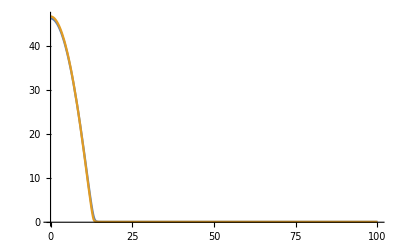

```mathematica
Plot[{Interpolation[Transpose@{fdSetupMC["UnitGrid"]*L/.params,fdSetupMC["nVec"]/.statSolMC}][x],n[x,T/1000]/.params/.initRunMC},{x,0,L/.params},
PlotRange->All]
```

#### Modes

```mathematica
{evalsMC,evecsMC}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianAS[
fdSetup,
params,
Join[Thread[fdSetup["etaVec"]->(eta/.statSolMC)],DeleteCases[statSolMC,eta->_]],
D[{0,-f},{{n,η}}],
"Reverse"->False
],-5,Method->{"Arnoldi",Tolerance->10^-20}],#[[1]]&];
```

```mathematica
evalsMC
```

0.0000944813812118148898513184875312976406299680406060498868751524025868180140631734410483593054437924074

Zero mode

```mathematica
{evalsMCS,evecsMCS}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianS[
fdSetup,
params,
Join[Thread[fdSetup["etaVec"]->(eta/.statSolMC)],DeleteCases[statSolMC,eta->_]],
D[{0,-f},{{n,η}}]
],-6,Method->{"Arnoldi",Tolerance->10^-20}],#[[1]]&];
```

```mathematica
evalsMCS
```

3.592624322521894320351469243158350768039324808976108883120899576625884829593964022397772512464401337×10^-115

```mathematica
massCompDModeNorm=evecsMC[[;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMC[[;;;;2]]])/.params;
massCompEtaModeNorm=evecsMC[[2;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMC[[;;;;2]]])/.params;
```

```mathematica
massDModeNorm=evecsMCS[[;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params;
dEtadM=Mean[evecsMCS[[2;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params];
```

```mathematica
lInt=(dx[fdSetupMC]*4*Total[massDModeNorm^2])^-1/.params
```

13.2477

```mathematica
σAnalytic=-dEtadM/(L/(2*Dv)+(1+Du/Dv)/(2lInt))/.params
```

0.0000863667

#### Plots

using Eq. (E4)

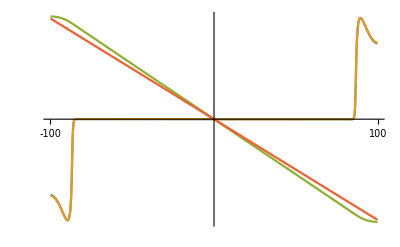

```mathematica
ListLinePlot[Transpose/@{{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-massCompDModeNorm,Reverse@massCompDModeNorm]},{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-massDModeNorm,Reverse@massDModeNorm]},
{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,100*Join[-massCompEtaModeNorm,Reverse@massCompEtaModeNorm]},
{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,100*Join[2*(L-fdSetupMC["UnitGrid"]*L)*σAnalytic/Dv/4/.params,-2*Reverse@(L-fdSetupMC["UnitGrid"]*L)*σAnalytic/Dv/4/.params]}},
PlotRange->All,
Ticks->{{-L,L}/.params,{-5,5}}]
```

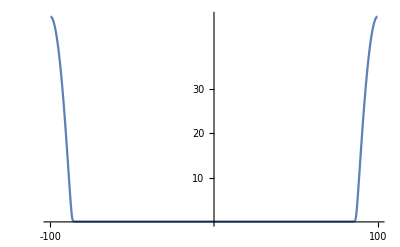

```mathematica
ListLinePlot[Transpose@{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[fdSetupMC["nVec"],Reverse@fdSetupMC["nVec"]]/.statSolMC},
PlotRange->All,
Ticks->{{-L,L}/.params,{10,20,30}}]
```